```mathematica
"Hello World"
```

Hello World

```mathematica
(11*17)+(4/2)
```

189

```mathematica
BaseForm[189,2]
```

```mathematica
Subscript["10111101", "2"]
2+√2
```

189

```mathematica
2+√2
N[0.5+√2]
```

2+√2

1.91421

```mathematica
N[√6,100]
```

2.449489742783178098197284074705891391965947480656670128432692567250960377457315026539859433104640235

```mathematica
3*4;100*100;Sqrt[4];Power[2,2];
```

```mathematica
4
```

4

```mathematica
Attributes[Power]
```

{Listable,NumericFunction,OneIdentity,Protected}

```mathematica
Module[{l=1,k=2,h=3},h √(k+l)+k+l]
```

```mathematica
3+3 √3
Clear[a,x,y]
```

```mathematica
3+3 √3
```

```mathematica
Head[a]
```

Symbol

```mathematica
Information[Head[a]]
```

```mathematica
RandomInteger[]
```

0

```mathematica
RandomInteger[10]
```

3

```mathematica
RandomInteger[1000]
```

45

```mathematica
Sin[90 Degree] + Cos[0 Degree]
```

2

```mathematica
Power[2,2]
```

4

```mathematica
d=Power[2,19]
```

524288

```mathematica
F=Sin[Pi]+ Cos[Pi]
```

-1

```mathematica
Clear[d,f]
```

```mathematica
Options[RandomWord]
```

{IncludeInflections→False,Language:>$Language}

```mathematica
$MachinePrecision
```

15.9546

```mathematica
Information[$MachinePrecision]
```

```mathematica
Information[MachinePrecision]
```

```mathematica
NumberForm[15.954589770191003,16]
```

```mathematica
DateObject[]
```

Thu 28 Apr 2022 23:13:47GMT+8.

```mathematica
Tomorrow
```

Day: Fri 29 Apr 2022

```mathematica
DateObject[{2022,5,1}]
```

```mathematica
DateObject[{2022,5,1},"Day","Gregorian",8.]

DateObject[Today,CalendarType ->"Julian"]
```

Day: Sun 1 May 2022

```mathematica
DateObject[{2022,4,15},"Day","Julian",8.]
RandomReal[{0,1},WorkingPrecision ->MachinePrecision]
```

Day: Thu 15 Apr 2022 (Juliancalendar)

0.903457

```mathematica
NumberForm[0.9034571969065586,16]
```

0.903457196906559

```mathematica
TimeZoneConvert[TimeObject[{17,0,0},TimeZone->"America/New_York"]]
```

Plot[Sin[x],{x,0,10}]



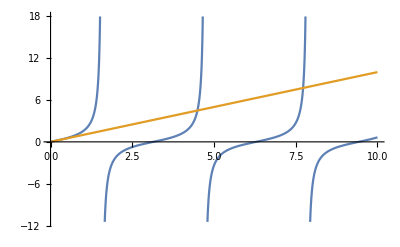

```mathematica
Plot[{Tan[x],x},{x,0,10}]
```

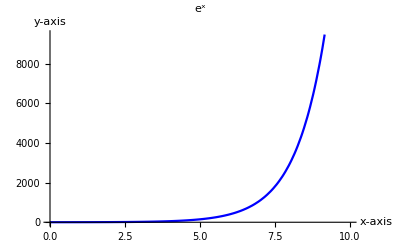

```mathematica
Plot[Exp[x],{x,0,10},PlotStyle ->{Blue},PlotLabel ->"e^x",AxesLabel->{"x-axis","y-axis"}]
```

```mathematica
1/3≥1/2
```

False

```mathematica
π≠-1
```

True

```mathematica
¬ 2==1
```

True

```mathematica
Expand[((x^2)+y^2)*(x+y)]
```

x^3+x^2 y+x y^2+y^3

```mathematica
Simplify[x^3+x^2 y+x y^2+y^3]
```

x^3+x^2 y+x y^2+y^3

```mathematica
FullSimplify[x^3+x^2 y+x y^2+y^3]
```

(x+y) (x^2+y^2)

```mathematica
Together[1/z+1/(z+1)-1/(z+2)]
```

```mathematica
(2+4 z+z^2)/(z (1+z) (2+z))
```

```mathematica
Apart[(2+4 z+z^2)/(z (1+z) (2+z))]
```

1/z+1/(1+z)-1/(2+z)

```mathematica
Solve[z^2+1==2,z]
```

{{z→-1},{z→1}}

```mathematica
z^2+1/.Rule[z,{1,-1}]
```

{2,2}

```mathematica
Information[Rule]
```

```mathematica
Solve[{x+y+z==2,6x-4y+5z==3,x+2y+2z==1},{x,y,z}]
```

{{x→3,y→10/9,z→-19/9}}

```mathematica
EQ1=x+y+z==2;EQ2=6 x-4 y+5 z==3;EQ3=x+2 y+2 z==1;
Solve[{EQ1,EQ2,EQ3},{x,y,z}]
```

{{x→3,y→10/9,z→-19/9}}

```mathematica
Solve[{x+y+z==a,6x-4y+5z==b,x+2y+2z==c},{x,y,z}]
```

{{x→2 a-c,y→1/9 (7 a-b-c),z→1/9 (-16 a+b+10 c)}}

DateObject::form: Argument TimeObject[{6,0,0.},Instant,8.] in DateObject cannot be interpreted as a date string format

TimeZoneConvert::notz: Argument America/Los Angeles in TimeZoneConvert is not a valid TimeZone specification.

DateObject::notgran: CalendarType→Julian is not a valid granularity specification for calendar Automatic.

```mathematica
Solve[EQ1&&EQ2,{x,y}]
```

{{x→1/10 (11-9 z),y→(9-z)/10}}

```mathematica
Solve[x^2+y^2==0||x-2y==1,x]
```

{{x→-ⅈ y},{x→ⅈ y},{x→1+2 y}}

```mathematica
Solve[z^-2+1==2&&z≠1,z]
```

{{z→-1}}

```mathematica
Reduce[Cos[x]==-1,x]
```

C[1]∈ℤ&&(x==-π+2 π C[1]||x==π+2 π C[1])

```mathematica
Reduce[α+β*α^2==E,α]
```

(β==0&&α==ⅇ)||(β≠0&&(α==(-1-√(1+4 ⅇ β))/(2 β)||α==(-1+√(1+4 ⅇ β))/(2 β)))

```mathematica
LinguisticAssistant   (*假装自己网不好才不出结果的，懂的都懂*)
```

Failure[…]

```mathematica
Clear[W];W:=RandomReal[];W
```

0.829921

```mathematica
W==W
```

False

```mathematica
Clear[W];W=RandomReal[];W
```

0.952328

```mathematica
W==W
```

True

```mathematica
(*  这里应该有:= 和 = 是不一样的结果*)
```

```mathematica
Timing[Power[10,100000000];]
```

{0.765625,Null}

```mathematica
Timing[10^100000000;]
```

{0.8125,Null}

```mathematica
AbsoluteTiming[10^100000000;]
```

{0.869941,Null}

```mathematica
TimeConstrained[10^100000000,0.1]
```

$Aborted

```mathematica
"Hello World" (*This is a comment*)
```

Hello World

```mathematica
ToString[23.423563]
```

23.4236

```mathematica
%//Head(*We use Head to knwo what type of objetc is*)
```

String

```mathematica
"Welcome to Mathematica"
```

Welcome to Mathematica

```mathematica
AtomQ["The sky is blue and tomorrow is expected to rain"]
```

True

```mathematica
AtomQ["Li is g"]
```

True

```mathematica
AtomQ["I am cool"]
```

True

```mathematica
Characters["Hello World"] (*Function that breaks the string into its characters*)
```

{H,e,l,l,o, ,W,o,r,l,d}

```mathematica
StringReplace["Hello this is a string ",{"h","H"}->"YourHero"]
(*This function repalce the string each time it appears for rule of the pattern,that is 4*)
```

YourHeroello tYourHerois is a string

```mathematica
StringJoin["Nice","to","have","you","back"]
```

Nicetohaveyouback

```mathematica
"Nice"<>"to"<>"have"<>"you"<>"back"
```

Nicetohaveyouback

```mathematica
StandardForm[1/x+x^2]
```

1/x+x^2

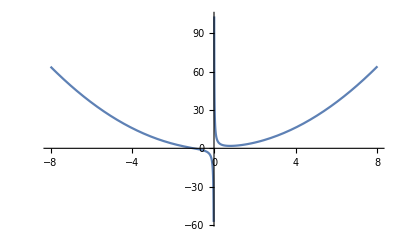

```mathematica
Plot[1/x+x^2,{x,-8,8}]
```

```mathematica
Subscript[a,x]
```

a_x

```mathematica
Trace[Plus[4,Times[Rational[1,2],t]]]
```

{{{Rational[1,2],1/2},t/2},4+t/2}

```mathematica
Information[Trace]
```

```mathematica
FullForm[Trace[Plus[4,Times[Rational[1,2],t]]]]
```

List[List[List[HoldForm[Rational[1,2]],HoldForm[Rational[1,2]]],HoldForm[Times[Rational[1,2],t]]],HoldForm[Plus[4,Times[Rational[1,2],t]]]]

```mathematica
RandomPolygon[]
```

Polygon[…]

```mathematica
Information[RandomPolygon]
```

```mathematica
?Head
```

```mathematica
?Rad*
```

```mathematica
StringJoin["hello","I am ",Jeff]
```

StringJoin::string: String expected at position 2 in helloI am <>Jeff.

helloI am <>Jeff

```mathematica
Power[x/0,2]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
$BaseDirectory
```

C:\ProgramData\Mathematica

```mathematica
$UserBaseDirectory
```

C:\Users\Administrator\AppData\Roaming\Mathematica

```mathematica
$InitialDirectory
```

C:\Users\Administrator\Documents

```mathematica
?Directory*
```

```mathematica
?*Directory
```

```mathematica
??List
```

```mathematica
{10,InputForm[10]}
```

{10,10}

```mathematica
{10//Accuracy,InputForm[10]//Precision}
```

{∞,∞}

```mathematica
{2.72//Precision,InputForm[2.72]}
```

{MachinePrecision,2.72}

```mathematica
{2.72123124123124123214325354376343241//Precision,InputForm[2.72213124124]}
```

{35.4348,2.72213124124}

```mathematica
a=MachinePrecision
```

MachinePrecision

```mathematica
N[a]
```

15.9546

```mathematica
Information[Accuracy]
```

```mathematica
{NumberQ[1/2],NumberQ[1],NumberQ[E]}
```

{True,True,False}

```mathematica
{1+0.2+1/2+1+11+1I}
```

{13.7+1. ⅈ}

```mathematica
Rationalize[2.72]
```

68/25

```mathematica
N[345/ π]
```

109.817

```mathematica
3~N~4
```

3.

```mathematica
3~N~5
```

3.

```mathematica
e//N         (*使用E， E才是自然指数我觉得*)
```

e

```mathematica
E~N~E
```

2.7

```mathematica
213123.223523423//N
```

213123.

```mathematica
N@E
```

2.71828

```mathematica
N@2397990123.12481024712
```

2.39799×10^9

```mathematica
$MachinePrecision               (*返回的值似乎只是一个例子，用来表示系统的机械精度是啥*)
```

15.9546

```mathematica
SetPrecision[π,17]
```

3.1415926535897932

```mathematica
SetPrecision[E,MachinePrecision]
```

2.71828

```mathematica
77/3`12
```

25.6666666667

```mathematica
IntegerDigits[234544553]
```

{2,3,4,5,4,4,5,5,3}

```mathematica
FromDigits[{2,3,4,5,4,4,5,5,3}]
```

234544553

```mathematica
FactorInteger[234544553]
```

{{3253,1},{72101,1}}

```mathematica
{RealDigits[321.4546554],RealDigits[N@E]}
```

{{{3,2,1,4,5,4,6,5,5,4,0,0,0,0,0,0},3},{{2,7,1,8,2,8,1,8,2,8,4,5,9,0,4,5},1}}

```mathematica
RealDigits[ReIm[113+2.7213I]]
```

{{{1,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0},3},{{2,7,2,1,3,0,0,0,0,0,0,0,0,0,0,0},1}}

```mathematica
RealDigits[321.4546,2]  (*二进制的321是有9个数的*)
```

{{1,0,1,0,0,0,0,0,1,0,1,1,1,0,1,0,0,0,1,1,0,0,0,0,0,1,0,1,0,1,0,1,0,0,1,1,0,0,1,0,0,1,1,0,0,0,0,1,1,0,0,0,0},9}

```mathematica
RealDigits[N@E,10,3]
```

{{2,7,1},1}

```mathematica
N@FromDigits[{{2,7,1,1},1}]
```

2.711

```mathematica
N@FromDigits[{{2,7,1,1},3}]
```

271.1

```mathematica
Cos[Pi]
```

-1

```mathematica
Sin[90 Degree]==Sin[90°]
```

True

```mathematica
N[Cosh[Pi]]
```

11.592

```mathematica
N[ArcTan[Pi]]   N[ArcSinh[45 Degree]]
```

0.910639

```mathematica
Log[E]
```

1

```mathematica
Factorial[12]
```

479001600

```mathematica
Round[8.9,2](*Rounds to 8 because it is the closest multiple of 2,2^3*)
```

8

```mathematica
Floor[Pi]
```

3

```mathematica
Ceiling[Pi]
```

4

```mathematica
⌊Pi⌋
```

3

```mathematica
⌈Pi⌉
```

4

```mathematica
Rationalize[N[E],0]
```

325368125/119696244

```mathematica
Max[9,8,7,0,3,12]
```

12

```mathematica
{x^2+1,"Dog",π}
List[1,P,Power[3,2]] (*Power[3,2] represents 3 raised to the power of 2*)
```

{1+x^2,Dog,π}

{1,P,9}

```mathematica
List["23.22","Dog",π,2,4,6,456.,56,2==3&&3==2]
```

{23.22,Dog,π,2,4,6,456.,56,False}

```mathematica
Echo[我感觉这个List和Python里面的数据形式有点像]
```

我感觉这个List和Python里面的数据形式有点像

我感觉这个List和Python里面的数据形式有点像

```mathematica
{1+I,π+π,"number 4",Sin[23 Degree],425+I-413-3I,24,4456.,"dog"+"cat"}
```

{1+ⅈ,2 π,number 4,Sin[23 °],12-2 ⅈ,24,4456.,cat+dog}

```mathematica
%//Head
```

List

```mathematica
Table["Soccer",{i,1,15}]
```

{Soccer,Soccer,Soccer,Soccer,Soccer,Soccer,Soccer,Soccer,Soccer,Soccer,Soccer,Soccer,Soccer,Soccer,Soccer}

```mathematica
Table[i^i,{i,1,5}]
```

{1,4,27,256,3125}

```mathematica
{Range[5],Table[h,{h,-6,2}]}
```

{{1,2,3,4,5},{-6,-5,-4,-3,-2,-1,0,1,2}}

```mathematica
Table[i+j+k,{i,1,4},{j,1,4},{k,1,4}]
```

{{{3,4,5,6},{4,5,6,7},{5,6,7,8},{6,7,8,9}},{{4,5,6,7},{5,6,7,8},{6,7,8,9},{7,8,9,10}},{{5,6,7,8},{6,7,8,9},{7,8,9,10},{8,9,10,11}},{{6,7,8,9},{7,8,9,10},{8,9,10,11},{9,10,11,12}}}

```mathematica
Table[i-j,{i,1,2},{j,1,2}]//Grid
```

0 | -1
1 | 0

```mathematica
Table[i+j,{i,1,2},{j,4,6}]//TableForm
```

5 | 6 | 7
6 | 7 | 8

```mathematica
Table[{i,j},{i,3},{j,i,3}]
```

{{{1,1},{1,2},{1,3}},{{2,2},{2,3}},{{3,3}}}

```mathematica
Table[{i,j},{i,3},{j,i,3}]//TableForm
```

1
1 | 1
2 | 1
3
2
2 | 2
3 | 
3
3 |  |

```mathematica
Table[{i,j},{i,2},{j,i++,2}]
```

{{{2,1},{2,2}},{{3,2}}}

```mathematica
x=0;x++;x (*applied on the current value and shown next time x is called*)
```

1

```mathematica
Clear[x];x=0;--x (*applied on the current value and shown when x is called*)
```

-1

```mathematica
x=0;--x (*applied on the current value and shown when x is called*)
```

-1

```mathematica
Table[RandomInteger[],{i,1,10}]/.1->2
```

{10.,0.,10.,0.,10.,10.,10.,0.,10.,10.}→2

```mathematica
Array[Cos[90 Degree],{3,3}]//Grid
```

0[1,1] | 0[1,2] | 0[1,3]
0[2,1] | 0[2,2] | 0[2,3]
0[3,1] | 0[3,2] | 0[3,3]

```mathematica
Array[F,{2,2}]//Grid
```

F[1,1] | F[1,2]
F[2,1] | F[2,2]

```mathematica
ConstantArray[π,5]
```

{π,π,π,π,π}

```mathematica
ConstantArray[π,{4,4}]
```

{{π,π,π,π},{π,π,π,π},{π,π,π,π},{π,π,π,π}}

```mathematica
ConstantArray[π,{4,4}]//MatrixForm
```

(π | π | π | π
π | π | π | π
π | π | π | π
π | π | π | π)

```mathematica
SparseArray[{{1,1},{2,2}}->{1,2}]
```

SparseArray[…]

```mathematica
MatrixForm[%]
```

(1 | 0
0 | 2)

```mathematica
SpArray=SparseArray[{{1,1}->"A",{2,2}->"A",{3,3}->"A",{4,4}->"A"},{4,4}]
```

SparseArray[…]

```mathematica
MatrixForm[%]
```

(A | 0 | 0 | 0
0 | A | 0 | 0
0 | 0 | A | 0
0 | 0 | 0 | A)

```mathematica
Normal[SpArray]
```

{{A,0,0,0},{0,A,0,0},{0,0,A,0},{0,0,0,A}}

```mathematica
Head[%]
```

List

```mathematica
{{"This","is","A"},{"Nested","List","."}}
```

{{This,is,A},{Nested,List,.}}

```mathematica
Table[Prime[i]+Prime[j],{i,1,3},{j,2,4}]
```

{{5,7,9},{6,8,10},{8,10,12}}

```mathematica
NestL=Table[Prime[i]+RandomReal[j],{i,1,3},{j,1,3}];
```

```mathematica
Length[NestL]
```

3

```mathematica
Dimensions[NestL]
```

{3,3}